```mathematica
SetDirectory[]
SetDirectory["Downloads"]
```

```mathematica
transData = TimeSeries[{Take[First[#], 3], #2}&@@@Rest[Flatten[Transpose[Import["bitcoinity_data(1).xlsx", "Data"]], 1]]];
```

```mathematica
data =FinancialData["BTC", {{2016, 7, 17},CurrentDate[]}];
allData = TimeSeriesResample[{data, transData}, "Intersection"];
returns = Differences@*Log@allData[[1, All, 2]];
```

```mathematica
ml = Predict[Flatten[Rest[allData[[2, All, 2] ]]]->  returns, PerformanceGoal->"Quality"];
```

```mathematica
var = Rest[allData[[2,All, 2]] ]-> returns;
```

```mathematica
pml = PredictorMeasurements[ml, var];
```

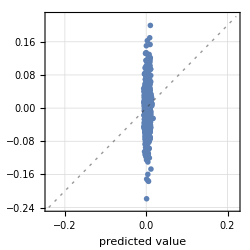
Predictor Measurements
Number of test examples | 1085
Standard deviation | 0.0422 ± 0.0015
Standard deviation baseline | 0.0424 ± 0.0015
Mean cross entropy | -1.75 ± 0.035
Single evaluation time | 2.01 ms/example
Batch evaluation speed | 2.14 examples/ms
-Graphics- |

1085

1085

```mathematica
pml["Report"]
```

```mathematica
ml["Report"]
```

```mathematica
allData[[1]]//Length
allData[[2]]//Length
returns//Length
```

1086

1086

1085

```mathematica
data =FinancialData["BTC", {{2016, 7, 17},CurrentDate[]}];
allData = TimeSeriesResample[{data, transData}, "Intersection"];
returns = Differences@*Log@allData[[1, All, 2]];
```

```mathematica
data[[2]];
```

```mathematica
data["Dates"]
```

{Mon 18 Jul 2016 00:00:00GMT-4.,Tue 19 Jul 2016 00:00:00GMT-4.,Wed 20 Jul 2016 00:00:00GMT-4.,Thu 21 Jul 2016 00:00:00GMT-4.,Fri 22 Jul 2016 00:00:00GMT-4.,Sat 23 Jul 2016 00:00:00GMT-4.,Sun 24 Jul 2016 00:00:00GMT-4.,Mon 25 Jul 2016 00:00:00GMT-4.,1072,Wed 3 Jul 2019 00:00:00GMT-4.,Thu 4 Jul 2019 00:00:00GMT-4.,Fri 5 Jul 2019 00:00:00GMT-4.,Sat 6 Jul 2019 00:00:00GMT-4.,Sun 7 Jul 2019 00:00:00GMT-4.,Mon 8 Jul 2019 00:00:00GMT-4.,Tue 9 Jul 2019 00:00:00GMT-4.,Wed 10 Jul 2019 00:00:00GMT-4.}
 |  |  |  |

gonna take bitcoin price and compare it to transaction history

```mathematica
LongShortTermMemoryLayer[1]
```

LongShortTermMemoryLayer[<>]